```mathematica
A=1;
f1[x_]:=A x^0.5
f2[x_]:=A (x+2)^0.5
f3[x_]:=A(x)^0.5+2
f4[x_]:=A(x+2)^0.5+2
```

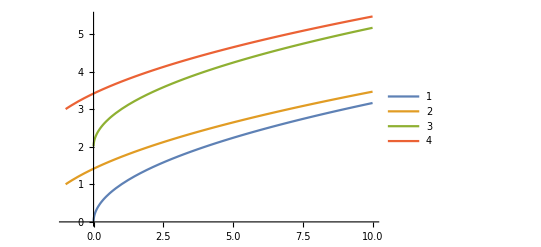

```mathematica
Plot[{f1[x],f2[x],f3[x],f4[x]},{x,-1,10},PlotLegends-> Automatic]
```

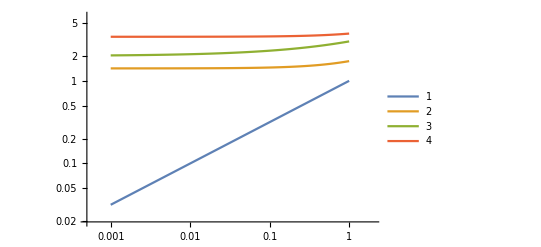

```mathematica
LogLogPlot[{f1[x],f2[x],f3[x],f4[x]},{x,0.001,1},PlotLegends-> Automatic]
```

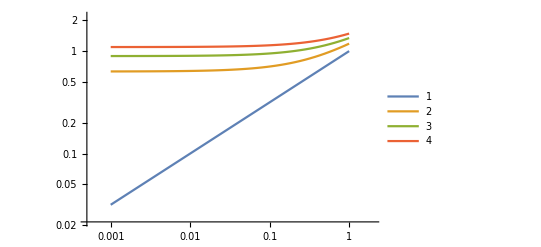

```mathematica
LogLogPlot[{f1[x],f1[x+0.4],f1[x+0.8],f1[x+1.2]},{x,0.001,1},PlotLegends-> Automatic]
```

```mathematica
powerLaw[x_,m_]:=x^m
```

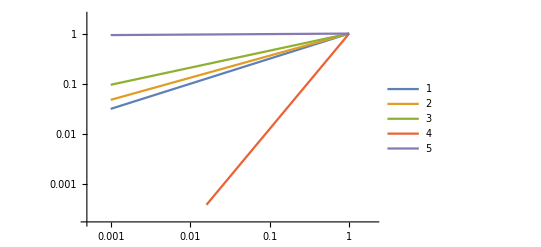

```mathematica
LogLogPlot[{powerLaw[x,0.5],powerLaw[x,0.44],powerLaw[x,0.34],powerLaw[x,1.9],powerLaw[x,0.01]},{x,0.001,1},PlotLegends-> Automatic]
```